# Diplomado en programación básica // Mathematica

Luis Gerardo Ramirez Archundia

01 de febrero de 2023

## Límites

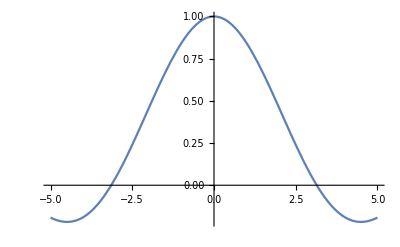

1

```mathematica
Plot[Sin[x]/x,{x,-5,5}]
Limit[Sin[x]/x,x->0]
```

## Derivadas

```mathematica
f[x_]=x^3+x^2+3 x
f'=D[f[x],x]
Plot[{f[x],f'},{x,-10,10}, PlotLabels->Automatic]
```

3 x+x^2+x^3

3+2 x+3 x^2

-Graphics-

## Integrales

```mathematica
f[x_]=Sin[x]
Integrate[f[x],{x,-1,1}]
```

Sin[x]

2/3

## Ejercicios

Realiza los siguientes límites

```mathematica
lim_(x->1) (5 x^3-4 x^2+2)/(x+3)
```

3/4

```mathematica
lim_(x->2) (5 x^3-4 x^2+1)/(4 x-7)
```

25

```mathematica
lim_(x->-3) (x^2-3 x+2)/(x-3)
```

-10/3

```mathematica
lim_(x->-3) 5/(x+3)^3
```

Indeterminate

```mathematica
lim_(x->∞) (4 x^3-2 x^2-1)/(6 x^3+5 x+2)
```

2/3

```mathematica
lim_(x->∞) 9/x^2
```

0

```mathematica
lim_(x->-5) (x^2-25)/(x+5)
```

-10

```mathematica
lim_(x->-2) (x^3+x-6)/(x+2)
```

Indeterminate

```mathematica
lim_(x->5) (x^2-7 x+2)/(x-5)
```

Indeterminate

```mathematica
lim_(y->-1) (y^3+1)/(y+1)
```

3

```mathematica
lim_(T->3) (T^2+T-12)/(T-3)
```

7

```mathematica
lim_(T->0) (√(T+2)-√2)/T
```

1/(2 √2)

Grafica la función mostrada en el límite Número 6 e implementa una tabla para verificar el límite

```mathematica
Plot[9/x^2,{x,-5,5},PlotLabels->Automatic]
Table[{x,9/x^2},{x,-2,2,0.1}]//TraditionalForm
```

-Graphics-

Power::infy: Infinite expression 1/0. encountered.

(-2. | 2.25
-1.9 | 2.49307
-1.8 | 2.77778
-1.7 | 3.11419
-1.6 | 3.51562
-1.5 | 4.
-1.4 | 4.59184
-1.3 | 5.32544
-1.2 | 6.25
-1.1 | 7.43802
-1. | 9.
-0.9 | 11.1111
-0.8 | 14.0625
-0.7 | 18.3673
-0.6 | 25.
-0.5 | 36.
-0.4 | 56.25
-0.3 | 100.
-0.2 | 225.
-0.1 | 900.
0. | ComplexInfinity
0.1 | 900.
0.2 | 225.
0.3 | 100.
0.4 | 56.25
0.5 | 36.
0.6 | 25.
0.7 | 18.3673
0.8 | 14.0625
0.9 | 11.1111
1. | 9.
1.1 | 7.43802
1.2 | 6.25
1.3 | 5.32544
1.4 | 4.59184
1.5 | 4.
1.6 | 3.51562
1.7 | 3.11419
1.8 | 2.77778
1.9 | 2.49307
2. | 2.25)

Implementa las siguientes expresiones en Mathematica

```mathematica
lim_(θ->0) Tan[θ]/Sin[θ]
```

1

```mathematica
lim_(y->2) (6 y^2-24 y+24)/(3 y-6)
```

0

```mathematica
Remove[f]
f[x_]=x^2
f'=(f[h+x]-f[x])/h
lim_(h->0) f'
```

x^2

((h+x)^2-x^2)/h

2 x

```mathematica
Remove[f]
f[x_]=x^2+5 x-3
lim_(h->0) (f[h+x]-f[x])/h
```

x^2+5 x-3

2 x+5

```mathematica
lim_(x->0) (√(x+2)-√2)/x
```

1/(2 √2)

```mathematica
lim_(x->2) √((2 x^2+3 x+4)/(x^3+1))
```

√2

```mathematica
lim_(y->-3) √((y^2-9)/(2 y^2+7 y+3))
```

√(6/5)

```mathematica
lim_(T->3/2) √((8 T^3-2 T)/(4 T^2-1))
```

√3

```mathematica
lim_(T->0) (2-√(4-T))/T
```

1/4

```mathematica
lim_(x->9) (x^2-81)/(3-√x)
```

-108

```mathematica
lim_(x->3) √((-(3 x^3)+5 x+2)/(x^2-1))
```

2 ⅈ √2

Confirmar los siguientes resultados para las derivadas

```mathematica
Remove[f]
f[x_]={k,x, a x+b,u[x]+v[x],k u[x],u[x] v[x],u[x]/v[x],x^n,Log[x],Log[x,a],Exp[x],a^x,Sin[x],Cos[x],Tan[x],Cot[x],ArcSin[x],ArcTan[x]};
f'=D[f[x],x];
Text["Tabla de derivadas"]
TableOfDerivadas={f[x],f'}//Transpose//TableForm
```

Tabla de derivadas

k | 0
x | 1
b+a x | a
u[x]+v[x] | u'[x]+v'[x]
k u[x] | k u'[x]
u[x] v[x] | v[x] u'[x]+u[x] v'[x]
u[x]/v[x] | u'[x]/v[x]-(u[x] v'[x])/v[x]^2
x^n | n x^(-1+n)
Log[x] | 1/x
Log[a]/Log[x] | -Log[a]/(x Log[x]^2)
ⅇ^x | ⅇ^x
a^x | a^x Log[a]
Sin[x] | Cos[x]
Cos[x] | -Sin[x]
Tan[x] | Sec[x]^2
Cot[x] | -Csc[x]^2
ArcSin[x] | 1/(√(1-x^2))
ArcTan[x] | 1/(1+x^2)

En el ejercicio anterior realiza una gráfica de la función y su derivada para cada expresión y ponles las
etiquetas correspondientes.

```mathematica
Remove[f]
TableOfPlots={}; (*Lista vacía donde irán los plots*)
f[x_]={1,x, x+1,x^3,Log[x],Log[x,10],Exp[x],3^x,Sin[x],Cos[x],Tan[x],Cot[x],ArcSin[x],ArcTan[x]}; (*Tabla de funciones*)
f'=D[f[x],x]; (*Tabla de derivadas*)
Text["Tabla de derivadas"];
TableOfDerivadas={f[x],f'}//Transpose//TableForm; (*Se juntan las dos tablas*)
AppendTo[ (*Pegamos cada plot al final de la lista vacía usando el comando Table para iterar cada plot*)
	TableOfPlots,Table[
						Plot[
								TableOfDerivadas[[1,n]],{x,-1,1},PlotLabels->{TableOfDerivadas[[1,n]]}, PlotStyle->Orange , ImageSize->Medium
								],{n,Length[f[x]]}
						]
			]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

Verifica las siguientes integrales

```mathematica
∫1ⅆu
```

u

```mathematica
∫u^n ⅆu
```

u^(n+1)/(n+1)

```mathematica
∫1/u ⅆu
```

Log[u]

```mathematica
∫a^u ⅆu
```

a^u/Log[a]

```mathematica
∫Sin[u]ⅆu
```

-Cos[u]

```mathematica
∫Cos[u]ⅆu
```

Sin[u]

```mathematica
∫Sec[u]^2 ⅆu
```

Tan[u]

```mathematica
∫Csc[u]^2 ⅆu
```

-Cot[u]

```mathematica
∫Tan[u] Sec[u]ⅆu
```

Sec[u]

```mathematica
∫Cot[u] Csc[u]ⅆu
```

-Csc[u]

```mathematica
∫Tan[u]ⅆu
```

-Log[Cos[u]]

```mathematica
∫Cot[u]ⅆu
```

Log[Sin[u]]

```mathematica
∫Sec[u]ⅆu
```

Log[Sin[u/2]+Cos[u/2]]-Log[Cos[u/2]-Sin[u/2]]

```mathematica
∫Csc[u]ⅆu
```

Log[Sin[u/2]]-Log[Cos[u/2]]

```mathematica
∫1/(√(a^2-u^2))ⅆu
```

ArcTan[u/(√(a^2-u^2))]

```mathematica
∫1/(a^2+u^2)ⅆu
```

ArcTan[u/a]/a

```mathematica
∫1/(u √(u^2-a^2))ⅆu
```

ArcTan[(√(u^2-a^2))/a]/a

```mathematica
∫1/(a^2-u^2)ⅆu
```

ArcTanh[u/a]/a

```mathematica
∫1/(u^2-a^2)ⅆu
```

-ArcTanh[u/a]/a

```mathematica
∫1/(√(a^2+u^2))ⅆu
```

1/2 Log[u/(√(a^2+u^2))+1]-1/2 Log[1-u/(√(a^2+u^2))]

```mathematica
∫1/(√(u^2-a^2))ⅆu
```

1/2 Log[u/(√(u^2-a^2))+1]-1/2 Log[1-u/(√(u^2-a^2))]

Realiza las siguientes operaciones

```mathematica
∫_0^∞ ⅇ^(-x^2)ⅆx
```

(√π)/2

```mathematica
∫_0^∞ x ⅇ^(-x^2)ⅆx
```

1/2

```mathematica
∫_0^∞ x^2 ⅇ^(-x^2)ⅆx
```

(√π)/4

```mathematica
∫_0^∞ x^3 ⅇ^(-x^2)ⅆx
```

1/2

```mathematica
∫_0^∞ x^4 ⅇ^(-x^2)ⅆx
```

(3 √π)/8

```mathematica
∫_0^∞ x^5 ⅇ^(-x^2)ⅆx
```

1